## Streamplot

```mathematica
Manipulate[StreamPlot[{-β M,-δ M C -γ C },{M,-10, 10},
 {C,-10,10}],{{δ,5},0,10}, {{β,1},0,10}, {{γ,3},0,10}]
```

## FindFit Exploration

```mathematica
SetDirectory[NotebookDirectory[]];
test  = Flatten[Import["Test.xlsx"],1]
```

{{0.,100.},{0.5,100.8},{1.,94.66},{1.5,90.94},{2.,82.92},{2.5,74.74},{3.,66.63},{3.5,57.91},{4.,49.18},{4.5,41.47},{5.,34.45},{5.5,27.69},{6.,22.29}}

```mathematica
ClearAll[δ ,t , γ]
```

```mathematica
test⟦1,2⟧
```

100.

100. ⅇ^(-0.172181 x)

{{0.,100.},{0.5,91.7511},{1.,84.1827},{1.5,77.2386},{2.,70.8673},{2.5,65.0215},{3.,59.658},{3.5,54.7369},{4.,50.2217},{4.5,46.079},{5.,42.278},{5.5,38.7905},{6.,35.5908}}

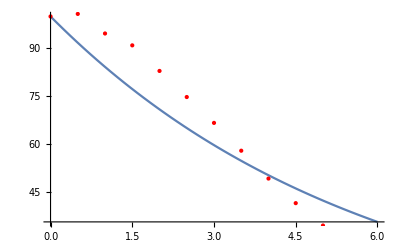

81.6551

```mathematica
FindFit[test,test⟦1,2⟧ Exp[-(δ t + γ)x],{δ ,t , γ},x];
test⟦1,2⟧Exp[-(δ t + γ)x]/.%
Table[{i,(%/.{x-> i})},{i,0,6,0.5}]
Show[Plot[%%,{x,0,6}],Graphics[{Red, Point[test]}]]
SquaredEuclideanDistance[%%ᵀ⟦2⟧ ,testᵀ⟦2⟧]/13
```

{δ→0.221433,t→-0.0808911,γ→0.00590772,β→0.144195,μ→-1.40519}

100. ⅇ^(5.46682 (1-ⅇ^(-0.144195 x)-0.144195 x)+0.0120043 x)

{{0.,100.},{0.5,99.216},{1.,95.8684},{1.5,90.3817},{2.,83.28},{2.5,75.1185},{3.,66.4269},{3.5,57.6673},{4.,49.211},{4.5,41.3294},{5.,34.1982},{5.5,27.909},{6.,22.4852}}

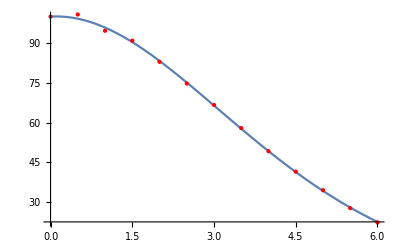

0.371095

```mathematica
FindFit[test,test⟦1,2⟧ Exp[-(δ* t+γ) x + (t μ)/β^2(1-ⅇ^(-β x)-β x)],{δ ,t , γ,β,μ},x]
test⟦1,2⟧ Exp[-(δ* t+γ) x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/.%
Table[{i,(%/.{x-> i})},{i,0,6,0.5}]
Show[Plot[%%,{x,0,6}],Graphics[{Red, Point[test]}]]
SquaredEuclideanDistance[%%ᵀ⟦2⟧ ,testᵀ⟦2⟧]/13
```

FindFit::fmmp: Machine precision is insufficient to achieve the requested accuracy or precision.

{t→0.341999,γ→-0.0142328,β→0.157172,μ→0.341999}

100. ⅇ^(4.73476 (1-ⅇ^(-0.157172 x)-0.157172 x)+0.0142328 x)

{{0.,100.},{0.5,99.2897},{1.,95.954},{1.5,90.4407},{2.,83.2967},{2.5,75.0954},{3.,66.3776},{3.5,57.6104},{4.,49.1643},{4.5,41.307},{5.,34.2084},{5.5,27.9546},{6.,22.5642}}

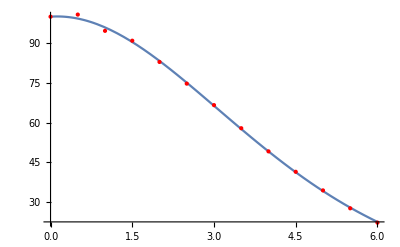

0.373595

```mathematica
FindFit[test,test⟦1,2⟧ Exp[-γ x + (t μ)/β^2(1-ⅇ^(-β x)-β x)],{t , γ,β,μ},x, Method->"Gradient"]
test⟦1,2⟧ Exp[-γ x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/.%
Table[{i,(%/.{x-> i})},{i,0,6,0.5}]
Show[Plot[%%,{x,0,6}],Graphics[{Red, Point[test]}]]
SquaredEuclideanDistance[%%ᵀ⟦2⟧ ,testᵀ⟦2⟧]/13
```